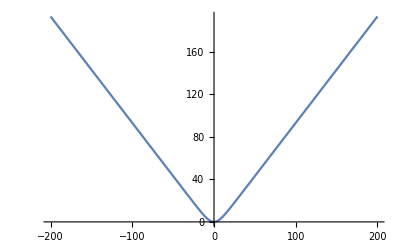

```mathematica
Plot[1/0.1 Log[Cosh[0.1x]], {x,-200,200}]
```

```mathematica
Plot3D[Re[Log[Cosh[x+I y]]], {x,-100,100},{y,-π,π}]
```

-Graphics3D-

```mathematica
Solve[Cosh[x] == 1,x]
```

{{x→ConditionalExpression[2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
Reduce[(I π)/h-(2 I π)/h D[ArcCosh[E^u],{u,1}] - π^2/(2 h^2 σ^2)u == 0,u]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(ⅈ π)/h-(2 ⅈ ⅇ^u π)/(√(-1+ⅇ^u) √(1+ⅇ^u) h)-(π^2 u)/(2 h^2 σ^2)==0,u]

```mathematica
Normal@Series[(ⅈ π)/h-(2 ⅈ ⅇ^u π)/(√(-1+ⅇ^u) √(1+ⅇ^u) h)-(π^2 u)/(2 h^2 σ^2), {u,0,1}]
```

(ⅈ π)/h-(ⅈ √2 π)/(h √u)-(ⅈ π √u)/(√2 h)-(π^2 u)/(2 h^2 σ^2)

```mathematica
Simplify[Solve[ψ == Log[Cosh[z]], z], Assumptions->{0<Im[ψ]< π}]
```

{{z→ConditionalExpression[-ArcCosh[ⅇ^ψ]+2 ⅈ π C[1],C[1]∈Integers]},{z→ConditionalExpression[ArcCosh[ⅇ^ψ]+2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
Log[Cosh[(I π)/2]]
```

-∞

```mathematica
D[(I π)/h u - (2 I π)/h u Log[1+Sqrt[1-E^(-2 u)]]- π^2/h^2 u^2/(4 σ^2),u]
```

(ⅈ π)/h-(2 ⅈ ⅇ^(-2 u) π u)/(√(1-ⅇ^(-2 u)) (1+√(1-ⅇ^(-2 u))) h)-(π^2 u)/(2 h^2 σ^2)-(2 ⅈ π Log[1+√(1-ⅇ^(-2 u))])/h

```mathematica
D[((I π)/h u - (2 I π)/h u Cosh[E^u]- π^2/h^2 u^2/(4 σ^2))/.u-> x+I y,x]
```

(ⅈ π)/h-(π^2 (x+ⅈ y))/(2 h^2 σ^2)-(2 ⅈ π Cosh[ⅇ^(x+ⅈ y)])/h-(2 ⅈ ⅇ^(x+ⅈ y) π (x+ⅈ y) Sinh[ⅇ^(x+ⅈ y)])/h

```mathematica
Simplify[ComplexExpand[Exp[((I π)/h u - (2 I π)/h u Cosh[E^u]- π^2/h^2 u^2/(4 σ^2))/.u-> x+I y]], Assumptions->{x>0,y>0,h>0,σ>0}]
```

ⅇ^((π (-π x^2+π y^2-4 h y σ^2+8 h y σ^2 Cos[ⅇ^x Sin[y]] Cosh[ⅇ^x Cos[y]]+8 h x σ^2 Sin[ⅇ^x Sin[y]] Sinh[ⅇ^x Cos[y]]))/(4 h^2 σ^2)) (Cos[1/(2 h^2 σ^2)π (π x y-2 h x σ^2+4 h x σ^2 Cos[ⅇ^x Sin[y]] Cosh[ⅇ^x Cos[y]]-4 h y σ^2 Sin[ⅇ^x Sin[y]] Sinh[ⅇ^x Cos[y]])]+ⅈ Sin[(π x)/h-(π^2 x y)/(2 h^2 σ^2)-(2 π x Cos[ⅇ^x Sin[y]] Cosh[ⅇ^x Cos[y]])/h+(2 π y Sin[ⅇ^x Sin[y]] Sinh[ⅇ^x Cos[y]])/h])

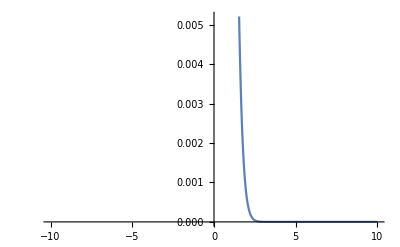

```mathematica
Plot[Exp[u-2 ArcCosh[E^u]- u^2], {u,-10,10}]
```

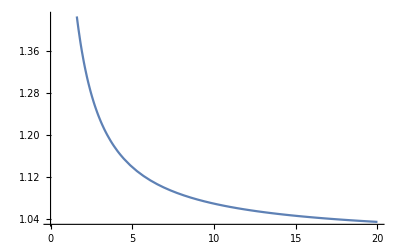

```mathematica
Plot[ArcCosh[E^u]/u,{u,0,20}]
```

```mathematica
D[(I π)/h u-(2 I π)/h Sqrt[u^2- ϵ]- π^2/h^2 u^2/(4 σ^2),u]
```

(ⅈ π)/h-(2 ⅈ π u)/(h √(u^2-ϵ))-(π^2 u)/(2 h^2 σ^2)

```mathematica
Solve[(ⅈ π)/h-(2 ⅈ π u)/(h √(u^2-ϵ))-(π^2 u)/(2 h^2 σ^2) == 0, u]/.h-> 0.01/.σ-> 1/.ϵ-> 0.0000000001
```

{{u→-4.2829×10^-16-5.7805×10^-6 ⅈ},{u→4.279×10^-16+5.76653×10^-6 ⅈ},{u→-5.84725×10^-19+0.0190986 ⅈ},{u→9.74543×10^-19-0.00636618 ⅈ}}

```mathematica
Series[ArcCosh[E^u],{u,0,2}]
```

(-1)^Floor[(π-Arg[(-1+ⅇ^u)/u]-Arg[u])/(2 π)] (√2 √u+u^(3/2)/(3 √2)+O[u]^(5/2))

```mathematica
Simplify[Exp[- β Cosh[x]], Assumptions->{β>0,x>0}]
```

ⅇ^(-β Cosh[x])

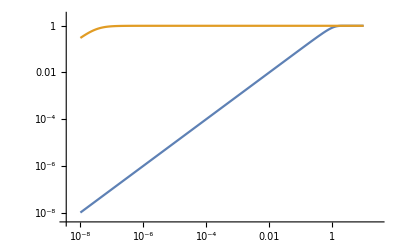

```mathematica
LogLogPlot[{Tanh[Sinh[x]],x/Sqrt[x^2+10^-15]},{x,10^-8,10}, PlotRange->All]
```

```mathematica
Plot3D[Re[Sqrt[(x+I y)^2+10^-15]],{x,-10^-1,10^-1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[(x+I y)Tanh[π/2 Sinh[x+I y]]],{x,-10,10},{y,-π/2,π/2}]
```

-Graphics3D-

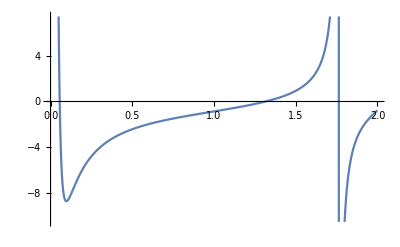

```mathematica
Plot[(Im[(x+I y)Tanh[π/2 Sinh[x+I y]]])/.y-> π/2-0.001,{x,0,2}]
```

```mathematica
ψ[z_] = z Tanh[π/2 Sinh[z]]
```

z Tanh[1/2 π Sinh[z]]

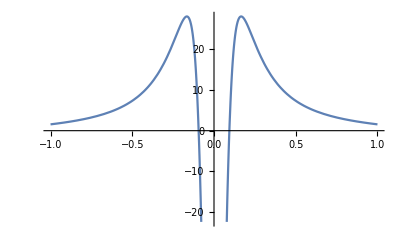

```mathematica
Plot[Re[(x+I y)Tanh[π/2 Sinh[x+I y]]]/.y-> π/2-0.1,{x,-1,1} ]
```

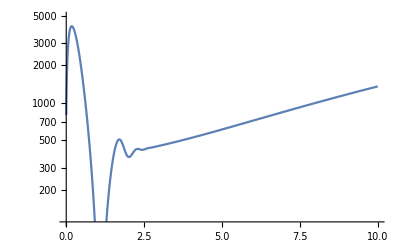

```mathematica
LogPlot[Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]])/.h-> 0.01/.σ-> 50/.y-> π/2-0.375],{x,0,10}]
```

```mathematica
ψ[I (π/2-0.4)]
```

-9.39369+0. ⅈ

```mathematica
Re[(-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2))/.h-> 0.01/.σ-> 1/.y-> π/2-0.3/.x-> -9.393685176278794]
```

2.13662×10^6

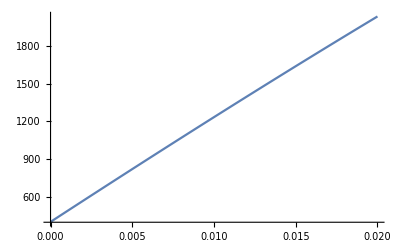

```mathematica
Plot[Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]])/.h-> 0.01/.σ-> 100/.y-> π/2-0.3],{x,0,0.02}]
```

```mathematica
((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[x+I y]])/.h-> 0.01/.σ-> 1/.y-> π/2-0.001
```

(0.+314.159 ⅈ) ((0.+1.5698 ⅈ)+x)-Log[ψ'[(0.+1.5698 ⅈ)+x]]-(0.+628.319 ⅈ) ψ[(0.+1.5698 ⅈ)+x]+24674. ψ[(0.+1.5698 ⅈ)+x]^2

```mathematica
ψ'[z]
```

1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2+Tanh[1/2 π Sinh[z]]

```mathematica
Normal@Series[(I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]], {x,0,2}]
```

-(π y)/h-Log[1/2 ⅈ (π y Cos[y] Sec[1/2 π Sin[y]]^2+2 Tan[1/2 π Sin[y]])]+(2 ⅈ π y Tan[1/2 π Sin[y]])/h+(π^2 y^2 Tan[1/2 π Sin[y]]^2)/(4 h^2 σ^2)+x ((ⅈ π)/h+(ⅈ (π Cos[y]+π Cos[y] Sec[1/2 π Sin[y]]^2-π y Sec[1/2 π Sin[y]]^2 Sin[y]+π^2 y Cos[y]^2 Sec[1/2 π Sin[y]]^2 Tan[1/2 π Sin[y]]+π Cos[y] Tan[1/2 π Sin[y]]^2))/(π y Cos[y] Sec[1/2 π Sin[y]]^2+2 Tan[1/2 π Sin[y]])+(π^2 y Cos[y]+2 π Tan[1/2 π Sin[y]]+π^2 y Cos[y] Tan[1/2 π Sin[y]]^2)/h-(ⅈ π^2 (π y^2 Cos[y] Tan[1/2 π Sin[y]]+2 y Tan[1/2 π Sin[y]]^2+π y^2 Cos[y] Tan[1/2 π Sin[y]]^3))/(4 h^2 σ^2))+x^2 (-(ⅈ (2 π^2 Cos[y]-π^2 y Sin[y]+π^3 y Cos[y]^2 Tan[1/2 π Sin[y]]+2 π^2 Cos[y] Tan[1/2 π Sin[y]]^2-π^2 y Sin[y] Tan[1/2 π Sin[y]]^2+π^3 y Cos[y]^2 Tan[1/2 π Sin[y]]^3))/(2 h)+1/2 (-((π Cos[y]+π Cos[y] Sec[1/2 π Sin[y]]^2-π y Sec[1/2 π Sin[y]]^2 Sin[y]+π^2 y Cos[y]^2 Sec[1/2 π Sin[y]]^2 Tan[1/2 π Sin[y]]+π Cos[y] Tan[1/2 π Sin[y]]^2)^2)/((π y Cos[y] Sec[1/2 π Sin[y]]^2+2 Tan[1/2 π Sin[y]])^2)+(-2 π y Cos[y] Sec[1/2 π Sin[y]]^2+π^3 y Cos[y]^3 Sec[1/2 π Sin[y]]^2-2 π Sin[y]-4 π Sec[1/2 π Sin[y]]^2 Sin[y]+2 π^2 Cos[y]^2 Tan[1/2 π Sin[y]]+4 π^2 Cos[y]^2 Sec[1/2 π Sin[y]]^2 Tan[1/2 π Sin[y]]-6 π^2 y Cos[y] Sec[1/2 π Sin[y]]^2 Sin[y] Tan[1/2 π Sin[y]]+3 π^3 y Cos[y]^3 Sec[1/2 π Sin[y]]^2 Tan[1/2 π Sin[y]]^2-2 π Sin[y] Tan[1/2 π Sin[y]]^2+2 π^2 Cos[y]^2 Tan[1/2 π Sin[y]]^3)/(2 (π y Cos[y] Sec[1/2 π Sin[y]]^2+2 Tan[1/2 π Sin[y]])))+1/(4 h^2 σ^2)π^2 (-Tan[1/2 π Sin[y]]^2-2 y (π Cos[y] Tan[1/2 π Sin[y]]+π Cos[y] Tan[1/2 π Sin[y]]^3)-1/4 y^2 (π^2 Cos[y]^2-2 π Sin[y] Tan[1/2 π Sin[y]]+4 π^2 Cos[y]^2 Tan[1/2 π Sin[y]]^2-2 π Sin[y] Tan[1/2 π Sin[y]]^3+3 π^2 Cos[y]^2 Tan[1/2 π Sin[y]]^4)))

```mathematica
D[Re[Simplify[ComplexExpand[(I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]]], Assumptions->{x>0,y>0,σ>0,h>0}]],x]
```

1/2 (-((2 Cosh[1/2 π Sinh[x-ⅈ y]]^2 (-π Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]+π Cos[y] Cosh[x] Sinh[π Cos[y] Sinh[x]]) (-π^2 x^2-2 ⅈ π^2 x y+π^2 y^2+4 ⅈ h π x σ^2-4 h π y σ^2-8 ⅈ h^2 σ^2 Arg[1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]] Cosh[1/2 π Sinh[x+ⅈ y]]^2-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)]+Cosh[π Sinh[x+ⅈ y]] (π (x+ⅈ y) (π x+ⅈ π y+4 ⅈ h σ^2)-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)])-8 ⅈ h π x σ^2 Sinh[π Sinh[x+ⅈ y]]+8 h π y σ^2 Sinh[π Sinh[x+ⅈ y]]))/(h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^3))+(π Cosh[x-ⅈ y] Cosh[1/2 π Sinh[x-ⅈ y]] Sinh[1/2 π Sinh[x-ⅈ y]] (-π^2 x^2-2 ⅈ π^2 x y+π^2 y^2+4 ⅈ h π x σ^2-4 h π y σ^2-8 ⅈ h^2 σ^2 Arg[1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]] Cosh[1/2 π Sinh[x+ⅈ y]]^2-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)]+Cosh[π Sinh[x+ⅈ y]] (π (x+ⅈ y) (π x+ⅈ π y+4 ⅈ h σ^2)-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)])-8 ⅈ h π x σ^2 Sinh[π Sinh[x+ⅈ y]]+8 h π y σ^2 Sinh[π Sinh[x+ⅈ y]]))/(h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^2)+(Cosh[1/2 π Sinh[x-ⅈ y]]^2 (-2 π^2 x-2 ⅈ π^2 y+4 ⅈ h π σ^2-8 ⅈ h π^2 x σ^2 Cosh[x+ⅈ y] Cosh[π Sinh[x+ⅈ y]]+8 h π^2 y σ^2 Cosh[x+ⅈ y] Cosh[π Sinh[x+ⅈ y]]-8 ⅈ h^2 π σ^2 Arg[1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]] Cosh[x+ⅈ y] Cosh[1/2 π Sinh[x+ⅈ y]] Sinh[1/2 π Sinh[x+ⅈ y]]-8 ⅈ h π σ^2 Sinh[π Sinh[x+ⅈ y]]+π Cosh[x+ⅈ y] (π (x+ⅈ y) (π x+ⅈ π y+4 ⅈ h σ^2)-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)]) Sinh[π Sinh[x+ⅈ y]]-(8 h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4 (-(((-π Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]+π Cos[y] Cosh[x] Sinh[π Cos[y] Sinh[x]]) ((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2))/(Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^5)+(2 (π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]]) (2 π Cos[y] Cos[π Cosh[x] Sin[y]] Cosh[x] Cosh[π Cos[y] Sinh[x]]+2 π Cos[y] Cosh[x] Cosh[2 π Cos[y] Sinh[x]]-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]+π Cos[y] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]]) Sinh[x]+2 π^2 x Cos[y] Cosh[x] Cosh[π Cos[y] Sinh[x]] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]+4 π^2 y Cos[1/2 π Cosh[x] Sin[y]] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2-4 π^2 y Cos[y] Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]+4 π^2 y Cos[y] Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]+4 π y Cosh[x] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+4 π^2 y Cos[1/2 π Cosh[x] Sin[y]] Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π x Cosh[x] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π^2 x Cos[π Cosh[x] Sin[y]] Sin[y]^2 Sinh[x]^2 Sinh[π Cos[y] Sinh[x]]+π Cos[y] Cosh[x] (2+Cosh[π Sinh[x-ⅈ y]]+Cosh[π Sinh[x+ⅈ y]]+π (x+ⅈ y) Cosh[x-ⅈ y] Sinh[π Sinh[x-ⅈ y]]+π (x-ⅈ y) Cosh[x+ⅈ y] Sinh[π Sinh[x+ⅈ y]]))+2 (π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]) (4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]+π Cos[y] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]]) Sinh[x]+2 π Cos[2 π Cosh[x] Sin[y]] Sin[y] Sinh[x]+4 π Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+2 π Cos[π Cosh[x] Sin[y]] Cosh[π Cos[y] Sinh[x]] Sin[y] Sinh[x]+2 π^2 y Cos[y] Cosh[x] Cosh[π Cos[y] Sinh[x]] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]-4 π^2 x Cos[1/2 π Cosh[x] Sin[y]] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2+4 π^2 x Cos[y] Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]-4 π^2 x Cos[y] Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]-4 π x Cosh[x] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2-4 π Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2-4 π^2 x Cos[1/2 π Cosh[x] Sin[y]] Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π Cos[y] Cosh[x] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π y Cosh[x] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π^2 y Cos[π Cosh[x] Sin[y]] Sin[y]^2 Sinh[x]^2 Sinh[π Cos[y] Sinh[x]]+π Cos[y] Cosh[x] (-ⅈ Cosh[π Sinh[x-ⅈ y]]+ⅈ Cosh[π Sinh[x+ⅈ y]]+π (-ⅈ x+y) Cosh[x-ⅈ y] Sinh[π Sinh[x-ⅈ y]]+π (ⅈ x+y) Cosh[x+ⅈ y] Sinh[π Sinh[x+ⅈ y]])))/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)))/((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)+Cosh[π Sinh[x+ⅈ y]] (π^2 (x+ⅈ y)+π (π x+ⅈ π y+4 ⅈ h σ^2)-(8 h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4 (-(((-π Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]+π Cos[y] Cosh[x] Sinh[π Cos[y] Sinh[x]]) ((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2))/(Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^5)+(2 (π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]]) (2 π Cos[y] Cos[π Cosh[x] Sin[y]] Cosh[x] Cosh[π Cos[y] Sinh[x]]+2 π Cos[y] Cosh[x] Cosh[2 π Cos[y] Sinh[x]]-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]+π Cos[y] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]]) Sinh[x]+2 π^2 x Cos[y] Cosh[x] Cosh[π Cos[y] Sinh[x]] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]+4 π^2 y Cos[1/2 π Cosh[x] Sin[y]] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2-4 π^2 y Cos[y] Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]+4 π^2 y Cos[y] Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]+4 π y Cosh[x] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+4 π^2 y Cos[1/2 π Cosh[x] Sin[y]] Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π x Cosh[x] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π^2 x Cos[π Cosh[x] Sin[y]] Sin[y]^2 Sinh[x]^2 Sinh[π Cos[y] Sinh[x]]+π Cos[y] Cosh[x] (2+Cosh[π Sinh[x-ⅈ y]]+Cosh[π Sinh[x+ⅈ y]]+π (x+ⅈ y) Cosh[x-ⅈ y] Sinh[π Sinh[x-ⅈ y]]+π (x-ⅈ y) Cosh[x+ⅈ y] Sinh[π Sinh[x+ⅈ y]]))+2 (π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]) (4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]+π Cos[y] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]]) Sinh[x]+2 π Cos[2 π Cosh[x] Sin[y]] Sin[y] Sinh[x]+4 π Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+2 π Cos[π Cosh[x] Sin[y]] Cosh[π Cos[y] Sinh[x]] Sin[y] Sinh[x]+2 π^2 y Cos[y] Cosh[x] Cosh[π Cos[y] Sinh[x]] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x]-4 π^2 x Cos[1/2 π Cosh[x] Sin[y]] Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2+4 π^2 x Cos[y] Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]-4 π^2 x Cos[y] Cosh[x] Cosh[1/2 π Cos[y] Sinh[x]] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]-4 π x Cosh[x] Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2-4 π Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2-4 π^2 x Cos[1/2 π Cosh[x] Sin[y]] Sin[y]^2 Sin[1/2 π Cosh[x] Sin[y]] Sinh[x]^2 Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π Cos[y] Cosh[x] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π y Cosh[x] Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π^2 y Cos[π Cosh[x] Sin[y]] Sin[y]^2 Sinh[x]^2 Sinh[π Cos[y] Sinh[x]]+π Cos[y] Cosh[x] (-ⅈ Cosh[π Sinh[x-ⅈ y]]+ⅈ Cosh[π Sinh[x+ⅈ y]]+π (-ⅈ x+y) Cosh[x-ⅈ y] Sinh[π Sinh[x-ⅈ y]]+π (ⅈ x+y) Cosh[x+ⅈ y] Sinh[π Sinh[x+ⅈ y]])))/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)))/((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2))-8 ⅈ h^2 σ^2 Cosh[1/2 π Sinh[x+ⅈ y]]^2 (π Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+1/2 π (x+ⅈ y) Sech[1/2 π Sinh[x+ⅈ y]]^2 Sinh[x+ⅈ y]-1/2 π^2 (x+ⅈ y) Cosh[x+ⅈ y]^2 Sech[1/2 π Sinh[x+ⅈ y]]^2 Tanh[1/2 π Sinh[x+ⅈ y]]) Arg'[1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]]))/(h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^2)) Re'[(Cosh[1/2 π Sinh[x-ⅈ y]]^2 (-π^2 x^2-2 ⅈ π^2 x y+π^2 y^2+4 ⅈ h π x σ^2-4 h π y σ^2-8 ⅈ h^2 σ^2 Arg[1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]] Cosh[1/2 π Sinh[x+ⅈ y]]^2-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)]+Cosh[π Sinh[x+ⅈ y]] (π (x+ⅈ y) (π x+ⅈ π y+4 ⅈ h σ^2)-2 h^2 σ^2 Log[((π Cos[y] Cosh[x] (2 y+(-ⅈ x+y) Cosh[π Sinh[x-ⅈ y]]+(ⅈ x+y) Cosh[π Sinh[x+ⅈ y]])+2 Cosh[π Cos[y] Sinh[x]] Sin[π Cosh[x] Sin[y]]+Sin[2 π Cosh[x] Sin[y]]+4 π x Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]-4 π x Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 π y Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]])^2+(π Cos[y] Cosh[x] (2 x+(x+ⅈ y) Cosh[π Sinh[x-ⅈ y]]+(x-ⅈ y) Cosh[π Sinh[x+ⅈ y]])-4 π y Cos[1/2 π Cosh[x] Sin[y]]^2 Cosh[1/2 π Cos[y] Sinh[x]]^2 Sin[y] Sinh[x]+4 π y Sin[y] Sin[1/2 π Cosh[x] Sin[y]]^2 Sinh[x] Sinh[1/2 π Cos[y] Sinh[x]]^2+2 Cos[π Cosh[x] Sin[y]] Sinh[π Cos[y] Sinh[x]]+2 π x Sin[y] Sin[π Cosh[x] Sin[y]] Sinh[x] Sinh[π Cos[y] Sinh[x]]+Sinh[2 π Cos[y] Sinh[x]])^2)/(4 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^4)])-8 ⅈ h π x σ^2 Sinh[π Sinh[x+ⅈ y]]+8 h π y σ^2 Sinh[π Sinh[x+ⅈ y]]))/(h^2 σ^2 (Cos[π Cosh[x] Sin[y]]+Cosh[π Cos[y] Sinh[x]])^2)]

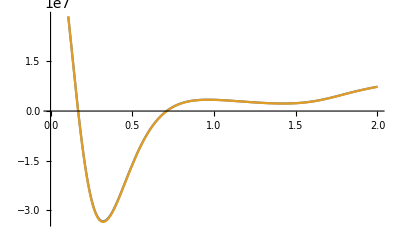

```mathematica
Plot[{Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]])/.h-> 0.0001/.σ-> 10/.y-> π/3],Re[( π^2/h^2 ψ[x+I y]^2/(4 σ^2))/.h-> 0.0001/.σ-> 10/.y-> π/3]},{x,0,2}]
```

```mathematica
NSolve[D[π^2/(0.001)^2 ψ[x+I (π/2-0.375)]^2/(4 (10)^2),x] == 0,x]
```

NSolve[(0.+77515.7 ⅈ) ((0.+1.1958 ⅈ)+x)^2 Cos[(1.1958+0. ⅈ)-ⅈ x] Sec[1/2 π Sin[(1.1958+0. ⅈ)-ⅈ x]]^2 Tan[1/2 π Sin[(1.1958+0. ⅈ)-ⅈ x]]-49348. ((0.+1.1958 ⅈ)+x) Tan[1/2 π Sin[(1.1958+0. ⅈ)-ⅈ x]]^2==0,x]

```mathematica
NSolve[Simplify[ψ'[x+I (π/2-0.375)]//Expand, Assumptions->{x>0}] == 0, x]
```

NSolve[((0.+1.87835 ⅈ)+1.5708 x) Cos[(1.1958+0. ⅈ)-ⅈ x] Sec[1/2 π Sin[(1.1958+0. ⅈ)-ⅈ x]]^2+ⅈ Tan[1/2 π Sin[(1.1958+0. ⅈ)-ⅈ x]]==0,x]

```mathematica
ψ[I π/3]//N
```

-4.90239

```mathematica
FindMinimum[ψ[x+I (π/2-0.375)]^2, {x,0.25}]
```

FindMinimum::nrnum: The function value -55.4254-23.2065 ⅈ is not a real number at {x} = {0.25}.

FindMinimum[ψ[x+ⅈ (π/2-0.375)]^2,{x,0.25}]

```mathematica
ψ[0.1+I π/3]
ψ[0.1-I π/3]
```

-4.23569+2.17682 ⅈ

-4.23569-2.17682 ⅈ

```mathematica
NSolve[Re[ψ[x+I (π/3)]] == 0, x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-Im[((ⅈ π)/3+x) Tan[1/2 π Cos[π/6+ⅈ x]]]==0,x]

```mathematica
NSolve[Normal@Series[ψ[x+I (π/3)],{x,0,2}]+Normal@Series[ψ[x-I (π/3)],{x,0,2}] == 0, x]
```

{{x→-0.262817},{x→0.262817}}

```mathematica
π/3//N
```

1.0472

```mathematica
Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[z]/.z-> x+I y])/.h-> 0.0001/.σ-> 10/.y-> π/3]/.x-> 0.2628172903431344
```

-2.89693×10^7

```mathematica
Re[((I π)/h(z)-2 π/h I ψ[z]+ π^2/h^2 ψ[z]^2/(4 σ^2)-Log[ψ'[z]])/.h-> 0.0001/.σ-> 10/.z-> x+I y/.y-> π/3]
```

ComplexExand[(0.+31415.9 ⅈ) ((ⅈ π)/3+x)-Log[1/2 π ((ⅈ π)/3+x) Sec[1/2 π Cos[π/6+ⅈ x]]^2 Sin[π/6+ⅈ x]+ⅈ Tan[1/2 π Cos[π/6+ⅈ x]]]+(62831.9+0. ⅈ) ((ⅈ π)/3+x) Tan[1/2 π Cos[π/6+ⅈ x]]-2.4674×10^6 ((ⅈ π)/3+x)^2 Tan[1/2 π Cos[π/6+ⅈ x]]^2]

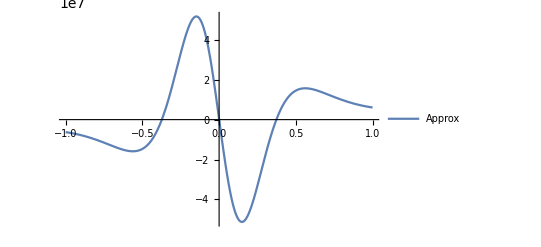

```mathematica
ψ[z_] = z Tanh[π/2 Sinh[z]];
Plot[{Im[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[z]/.z-> x+I y])/.h-> 0.0001/.σ-> 10/.y-> π/3]}, {x,-1,1}, PlotLegends->{"Approx", "Exact"}]
```

```mathematica
Re[Normal@Series[ π^2/h^2 ψ[x+I π/3]^2/(4 σ^2),{x,0.2628172903431344,2} ]/.h-> 0.0001/.σ-> 10]
```

-2.9174×10^7+Re[(-1.59447×10^8+2.97807×10^8 ⅈ) (-0.262817+x)+(1.58816×10^9+1.69966×10^8 ⅈ) (-0.262817+x)^2]

```mathematica
Plot[%5, {x,0,1}]
```

Out::intm: Machine-sized integer expected at position 1 in Out[5.].

General::stop: Further output of Out::intm will be suppressed during this calculation.

-Graphics-

```mathematica
Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[z]/.z-> x+I y])/.h-> 0.0001/.σ-> 10/.y-> π/3]
```

Re[(0.+31415.9 ⅈ) ((ⅈ π)/3+x)-Log[1/2 π ((ⅈ π)/3+x) Sec[1/2 π Cos[π/6+ⅈ x]]^2 Sin[π/6+ⅈ x]+ⅈ Tan[1/2 π Cos[π/6+ⅈ x]]]+(62831.9+0. ⅈ) ((ⅈ π)/3+x) Tan[1/2 π Cos[π/6+ⅈ x]]-2.4674×10^6 ((ⅈ π)/3+x)^2 Tan[1/2 π Cos[π/6+ⅈ x]]^2]

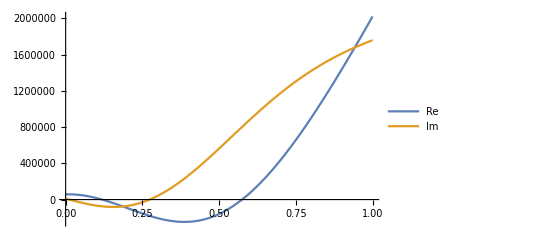

```mathematica
Plot[{Re[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]])/.h-> 0.0001/.σ-> 10/.y-> π/10],Im[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]])/.h-> 0.0001/.σ-> 10/.y-> π/10]},{x,0,1}, PlotLegends->{"Re", "Im"}]
```

```mathematica
xval = Re[ψ[x+I π/20]^2]/.x-> 0.2628172903431344
```

-0.00940461

```mathematica
f[x_] = Re[Normal@Series[ψ[x+I π/20]^2, {x,xval,4}]];
```

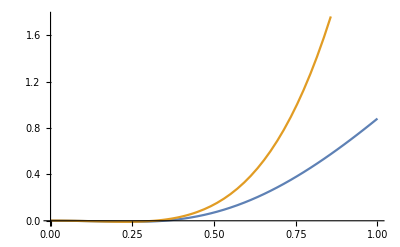

```mathematica
Plot[{Re[ψ[x+I π/20]^2], f[x]},{x,0,1}]
```

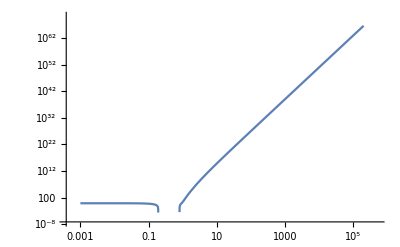

```mathematica
LogLogPlot[f[x],{x,0.001,200000}]
```

```mathematica
NSolve[D[Re[ψ[x+I π/5]^2], x] == 0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-(-ⅈ π ((ⅈ π)/5+x)^2 Cos[π/5-ⅈ x] Sec[1/2 π Sin[π/5-ⅈ x]]^2 Tan[1/2 π Sin[π/5-ⅈ x]]+2 ((ⅈ π)/5+x) Tan[1/2 π Sin[π/5-ⅈ x]]^2) Re'[((ⅈ π)/5+x)^2 Tan[1/2 π Sin[π/5-ⅈ x]]^2]==0,x]

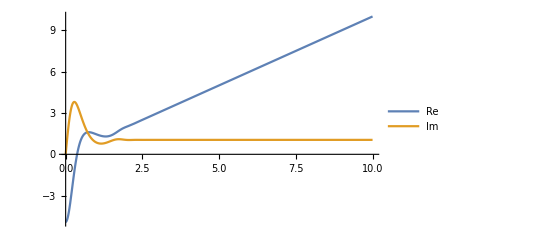

```mathematica
Series[Re[ψ[x+I π/5]^2], {x,}]
```

```mathematica
NSolve[Normal@Series[ψ[x+I (π/5)],{x,0,2}]+Normal@Series[ψ[x-I (π/5)],{x,0,2}] == 0, x]
```

{{x→-0.360776},{x→0.360776}}

```mathematica
Series[(I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[ψ'[ x+I y]],{x,}]
```

```mathematica
NSolve[Normal@Series[ψ[x+I π/3],{x,0,2}]+Normal@Series[ψ[x-I π/3],{x,0,2}] == 0,x]
```

{{x→-0.262817},{x→0.262817}}

```mathematica
NSolve[Normal@Series[ψ[x+I (π/3)],{x,0,10}]+Normal@Series[ψ[x-I (π/3)],{x,0,10}] == 0, x]
```

{{x→-0.362242-0.151052 ⅈ},{x→-0.362242+0.151052 ⅈ},{x→-0.342592},{x→-0.25639-0.348493 ⅈ},{x→-0.25639+0.348493 ⅈ},{x→0.25639-0.348493 ⅈ},{x→0.25639+0.348493 ⅈ},{x→0.342592},{x→0.362242-0.151052 ⅈ},{x→0.362242+0.151052 ⅈ}}

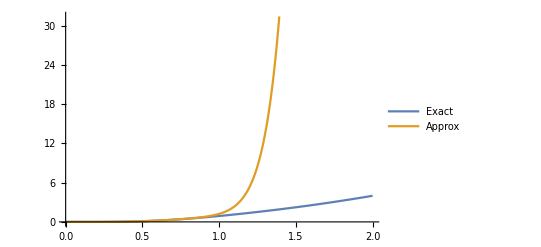

```mathematica
Plot[{Re[ψ[x+I π/50]^2],f[x]},{x,0,2}, PlotLegends->{"Exact", "Approx"}]
```

```mathematica
f[x_] = ComplexExpand[Re[Normal@Series[ψ[x+I π/50]^2, {x,0.1,12}]]];
```

```mathematica
NIntegrate[Exp[-f[x]],{x,0,Infinity}]
```

0.833038

```mathematica
NIntegrate[Exp[-Re[Normal@Series[((I π)/h(x+I y)-2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[π/h ψ'[ x+I y]])/.y-> π/50,{x,0.1,12}]/.h-> 0.001/.σ-> 1]],{x,0,Infinity}]
```

5.06112951692187×10^346

```mathematica
NIntegrate[Exp[-Re[Normal@Series[(-(I π)/h(x+I y)+2 π/h I ψ[x+I y]+ π^2/h^2 ψ[x+I y]^2/(4 σ^2)-Log[π/h ψ'[ x+I y]])/.y-> -π/50,{x,0.1,12}]/.h-> 0.001/.σ-> 1]],{x,0,Infinity}]
```

5.06112951692187×10^346

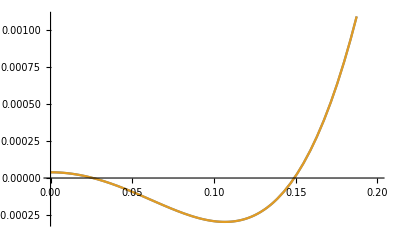

```mathematica
Plot[{Re[ψ[x+I y]^2/.y-> -π/50],Re[ψ[x+I y]^2/.y-> π/50]},{x,0,0.2}]
```

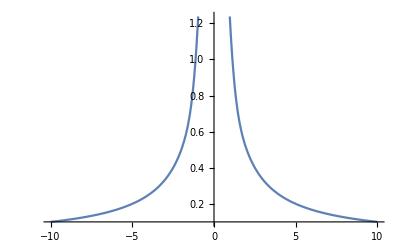

```mathematica
Plot[1/x ψ'[x], {x,-10,10}]
```

```mathematica
Plot[Abs[ψ[x] BesselJ[0,ψ[x]] Exp[- (ψ^2)[x]]ψ'[x] Exp[I x]], {x,-1,1}]
```

-Graphics-

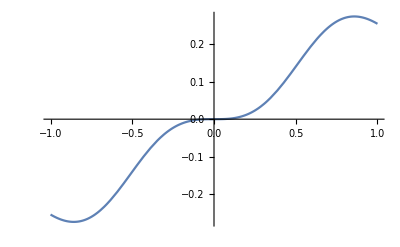

```mathematica
Plot[Re[ψ[x]BesselJ[0,ψ[x]]Exp[- ψ[x]^2]Exp[I x]], {x,-1,1}]
```

```mathematica
ψ'[0.1+I π/3]
```

12.5163+18.4372 ⅈ

```mathematica
ψ'[-0.1-I π/3]
```

-12.5163-18.4372 ⅈ

```mathematica
exp[z_] = (-2 π I z)/h+Log[π/h Sqrt[ψ[z]]]+Log[π/h ψ'[z]]- (ψ[z]^2 π^2)/(4 σ^2 h^2)- I π/h ψ[z]
```

-(2 ⅈ π z)/h+Log[(π √(z Tanh[π Sinh[z]]))/h]+Log[(π (π z Cosh[z] Sech[π Sinh[z]]^2+Tanh[π Sinh[z]]))/h]-(ⅈ π z Tanh[π Sinh[z]])/h-(π^2 z^2 Tanh[π Sinh[z]]^2)/(4 h^2 σ^2)

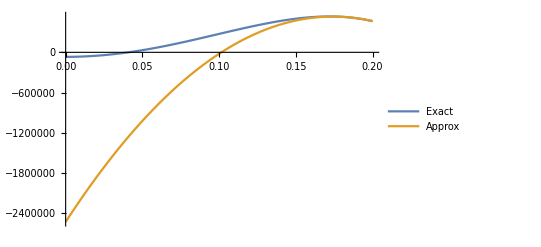

```mathematica
Plot[{Re[exp[z]/.z-> x+ I π/30/.h-> 0.0001/. σ-> 1],Re[approx/.h-> 0.0001/. σ-> 1]}, {x,0,0.2},PlotLegends->{"Exact","Approx"}]
```

```mathematica
Plot[{Re[%263/.h-> 0.0001/. σ-> 1]}, {x,-0.3,0.3},PlotLegends->{"Exact","Approx"}]
```

$Aborted

```mathematica
Exp[%263/.h-> 0.0001/. σ-> 1]
```

ⅇ^(-74278.1+(0.+2.85775×10^6 ⅈ) x+4.15267×10^7 x^2-(0.+2.73902×10^8 ⅈ) x^3-(7.4672×10^8+0. ⅈ) x^4+(0.+5.52517×10^8 ⅈ) x^5+(1.04739×10^9+0. ⅈ) x^6-(0.+7.23123×10^8 ⅈ) x^7-(1.08077×10^9+0. ⅈ) x^8+(0.+7.38891×10^8 ⅈ) x^9+(9.34351×10^8+0. ⅈ) x^10)

```mathematica
NIntegrate[Exp[%276/.h-> 0.001/. σ-> 1],{x,-Infinity,Infinity} ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.166287}. NIntegrate obtained -2.25301050525313×10^2480+2.51411959674564×10^2480 ⅈ and 4.679139429095×10^2480 for the integral and error estimates.

-2.25301050525313×10^2480+2.51411959674564×10^2480 ⅈ

```mathematica
approx = Normal@Series[exp[z]/.z-> x+I π/30,{x,0.19,2}];
```

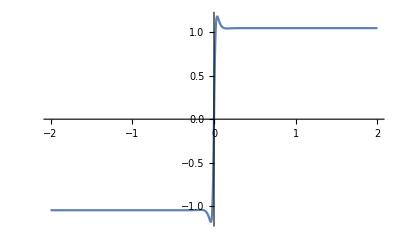

```mathematica
Plot[Im[(x+I π/3) Tanh[10 π Sinh[x+I π/3]]], {x,-2,2}]
```

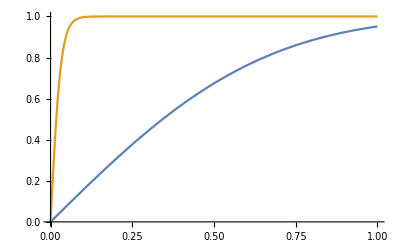

```mathematica
Plot[{Tanh[π/2 Sinh[x]],Tanh[10π Sinh[x]]},{x,0,1}]
```

```mathematica
Integrate[Exp[approx],{x,-Infinity,Infinity}, Assumptions->{h>0,σ>0}]
```

(1. ⅇ^(((0.000248877+0.000168148 ⅈ)+(0.0503197+0.0499785 ⅈ) h σ^2+(1.56955-2.2701 ⅈ) h^3 σ^4+(2.74792-1.72544 ⅈ) h^4 σ^4+h^2 ((0.0896808+0.100181 ⅈ) σ^2-(0.228022+0.387136 ⅈ) σ^4))/(h^2 σ^2 ((-0.0181376+0.0688993 ⅈ)-(0.143283-0.141823 ⅈ) h σ^2+1. h^2 σ^2))) ((-0.00900589-0.00746704 ⅈ)-(0.0535512-0.175278 ⅈ) h σ^2-(0.380112-0.28235 ⅈ) h^2 σ^2+((-1.29672×10^-18-1.91362×10^-19 ⅈ)-(1.47952×10^-17+7.48323×10^-18 ⅈ) h σ^2-(4.76909×10^-17+1.52123×10^-18 ⅈ) h^2 σ^2) Erfi[((-0.11418+0.175952 ⅈ)+(3.23299+0.587929 ⅈ) h σ^2+(5.821+6.17979 ⅈ) h^2 σ^2)/(h^2 √((12.9147-18.0724 ⅈ)+(0.712627+4.42108 ⅈ)/h+(1.01093+1.2176 ⅈ)/(h^2 σ^2)) σ^2)]))/(h^2 √((12.9147-18.0724 ⅈ)+(0.712627+4.42108 ⅈ)/h+(1.01093+1.2176 ⅈ)/(h^2 σ^2)) ((0.00586483+0.0240007 ⅈ)+(0.311521-0.229721 ⅈ) h σ^2+1. h^2 σ^2))

```mathematica
approx
```

(0.847902-1.32071 ⅈ)/h+(-0.19+x)^2 ((-12.9147+18.0724 ⅈ)-(0.712627+4.42108 ⅈ)/h-(1.01093+1.2176 ⅈ)/(h^2 σ^2))+(-0.19+x) ((7.45199-4.77448 ⅈ)+(0.905061-1.86281 ⅈ)/h-(2 ⅈ π)/h-(0.0322516+0.234329 ⅈ)/(h^2 σ^2))+(0.004992-0.0120515 ⅈ)/(h^2 σ^2)+Log[(0.747095+0.399333 ⅈ)/h]+Log[(1.86281+0.905061 ⅈ)/h]

```mathematica
Plot3D[Log10[(h/π)^2 Abs[%315]],{h,0.0001,0.01},{σ,0.1,10}]
```

-Graphics3D-

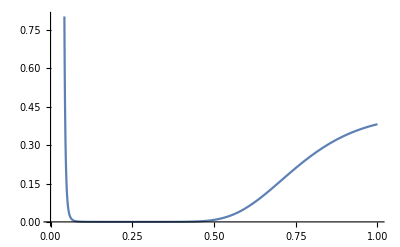

```mathematica
Plot[(h/π)^2 Abs[%315]/.σ-> 1, {h,0.00001,1}]
```

```mathematica
Abs[%315]/.h-> 0.0001/.σ-> 1
```

3.47282086900863×10^62626

```mathematica
Plot[Re[approx/.h-> 0.0001/.σ-> 1],{x,0.01,0.01}]
```

Plot::plld: Endpoints for x in {x,0.01,0.01} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[Re[approx/.h→0.0001/.σ→1],{x,0.01,0.01}]

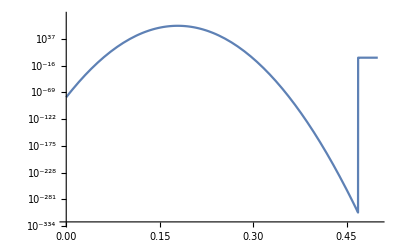

```mathematica
LogPlot[Abs[Exp[approx/.h-> 0.01/. σ-> 1]], {x,0,0.5}]
```

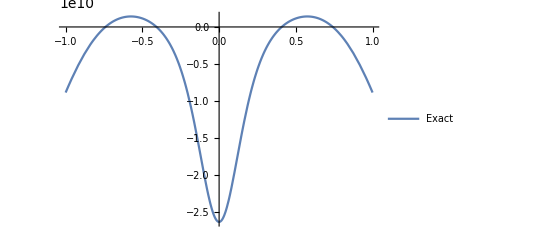

```mathematica
Plot[{Re[exp[z]/.z-> x- I π/4/.h-> 0.00001/. σ-> 1]}, {x,-1,1},PlotLegends->{"Exact","Approx"}]
```

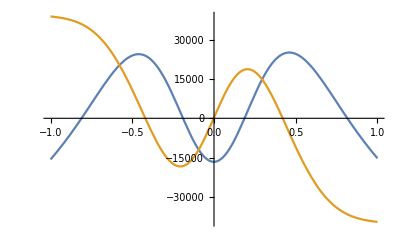

```mathematica
Plot[{Re[exp[z]/.z-> x+I π/5/.h-> 0.01/.σ-> 1],Im[exp[z]/.z-> x+I π/5/.h-> 0.01/.σ-> 1]},{x,-1,1}]
```

```mathematica
approx = Normal@Series[exp[z]/.z-> x+I π/30,{x,0,4}];
```

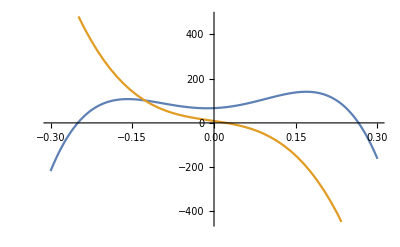

```mathematica
Plot[{Re[approx/.σ-> 1/.h-> 0.01],Im[approx/.σ-> 1/.h-> 0.01]},{x,-0.3,0.3}]
```

```mathematica
NIntegrate[Exp[approx/.h-> 0.001/.σ-> 10],{x,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.202573}. NIntegrate obtained 1.53923449995388×10^377+6.79652545589261×10^376 ⅈ and 1.10838562301817×10^378 for the integral and error estimates.

1.53923449995387×10^377+6.79652545589261×10^376 ⅈ

```mathematica
NIntegrate[Exp[exp[x+I π/3]/.h-> 0.01/.σ-> 1], {x,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.319615}. NIntegrate obtained -1.17084841527007×10^146521-1.32815934749564×10^146521 ⅈ and 1.13095192282215×10^146521 for the integral and error estimates.

-1.17084841527007×10^146521-1.32815934749564×10^146521 ⅈ

```mathematica
exp[x+I π/30]
```

-(2 ⅈ π ((ⅈ π)/30+x))/h+Log[(π (1/2 π ((ⅈ π)/30+x) Cos[π/30-ⅈ x] Sec[1/2 π Sin[π/30-ⅈ x]]^2+ⅈ Tan[1/2 π Sin[π/30-ⅈ x]]))/h]+Log[(π √(ⅈ ((ⅈ π)/30+x) Tan[1/2 π Sin[π/30-ⅈ x]]))/h]+(π ((ⅈ π)/30+x) Tan[1/2 π Sin[π/30-ⅈ x]])/h+(π^2 ((ⅈ π)/30+x)^2 Tan[1/2 π Sin[π/30-ⅈ x]]^2)/(4 h^2 σ^2)

```mathematica
exp[z_] = (-2 π I z)/h+Log[π/h Sqrt[ψ[z]]]+Log[π/h ψ'[z]]- (ψ[z] π)/h λ- I π/h ψ[z]
```

-(2 ⅈ π z)/h+Log[(π √(z Tanh[1/2 π Sinh[z]]))/h]+Log[(π (1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2+Tanh[1/2 π Sinh[z]]))/h]-(ⅈ π z Tanh[1/2 π Sinh[z]])/h-(π z λ Tanh[1/2 π Sinh[z]])/h

```mathematica
ψ[z_] = z Tanh[ π Sinh[z]]
NIntegrate[Exp[exp[x-I π/10]]/.h-> 0.01/.λ-> 1,{x,-1,1}]
```

z Tanh[π Sinh[z]]

-6.69751×10^-45+1.22649×10^-43 ⅈ

```mathematica
NIntegrate[(ψ[x+I π/30]BesselJ[0,π/h ψ[x+I π/30]]ψ'[x+π/30]Exp[-2 π I (x+I π/30)/h]Exp[- ψ[x+I π/30]])/.h-> 0.1/,{x,-1,1}]
```

NIntegrate::inumr: The integrand ⅈ ⅇ^(-(2 ⅈ π ((ⅈ π)/30+x))/h) ((ⅈ π)/30+x) BesselJ[0,(ⅈ π ((ⅈ π)/30+x) Tan[π Sin[Times[«2»]+Times[«2»]]])/h] Tan[π Sin[π/30-ⅈ x]] (π (π/30+x) Cosh[π/30+x] Sech[π Sinh[Plus[«2»]]]^2+Tanh[π Sinh[π/30+x]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate[ψ[x+(ⅈ π)/30] BesselJ[0,(π ψ[x+(ⅈ π)/30])/h] ψ'[x+π/30] Exp[-(2 π ⅈ (x+(ⅈ π)/30))/h],{x,-1,1}]